### Import data

```mathematica
Φ=ExternalEvaluate["Python","import numpy as np
np.load('/Users/yanbozhang/项目 & 存档/01 科研项目/IIT/IIT and Sensitivity/Muti_model_Phi.npy').tolist()"];
```

```mathematica
S=ExternalEvaluate["Python","import numpy as np
np.load('/Users/yanbozhang/项目 & 存档/01 科研项目/IIT/IIT and Sensitivity/Muti_model_sensitivites.npy').tolist()"];
```

## Plot

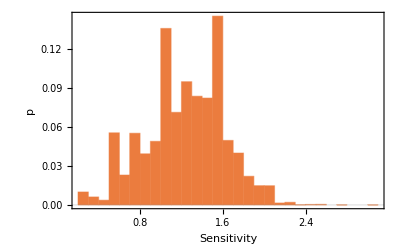

```mathematica
Histogram[Flatten[S],Automatic,"Probability",PlotTheme->"Scientific",FrameLabel->{"Sensitivity",p}]
```

### For all data

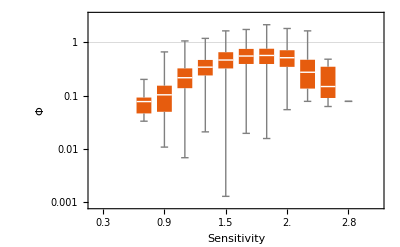

```mathematica
data=GatherBy[{Flatten[S,1],Mean/@Flatten[Φ,1]}ᵀ,⌊5#⟦1⟧⌋&];
data=SortBy[data,#⟦1,1⟧&];
imgAllBoxWhisker=BoxWhiskerChart[#ᵀ⟦2⟧&/@data,ChartLabels->(Round[#⟦1,1⟧,0.1]&/@data),PlotRange->All,PerformanceGoal->"Speed",PlotTheme->"Scientific",ScalingFunctions->"Log",FrameLabel->{"Sensitivity","Φ"}]
```

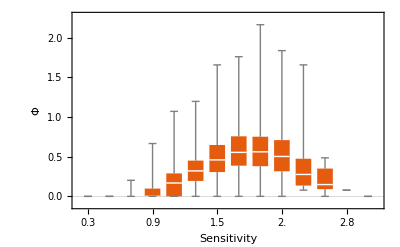

```mathematica
data=GatherBy[{Flatten[S,1],Mean/@Flatten[Φ,1]}ᵀ,⌊5#⟦1⟧⌋&];
data=SortBy[data,#⟦1,1⟧&];
imgAllBoxWhisker=BoxWhiskerChart[#ᵀ⟦2⟧&/@data,ChartLabels->(Round[#⟦1,1⟧,0.1]&/@data),PlotRange->All,PerformanceGoal->"Speed",PlotTheme->"Scientific",FrameLabel->{"Sensitivity","Φ"}]
```

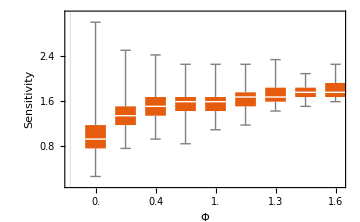

```mathematica
data2=GatherBy[{Mean/@Flatten[Φ,1],Flatten[S,1]}ᵀ,⌊5#⟦1⟧⌋&];
data2=SortBy[data2,#⟦1,1⟧&];
imgAllBoxWhisker2=BoxWhiskerChart[#ᵀ⟦2⟧&/@data2,ChartLabels->(Round[#⟦1,1⟧,0.1]&/@data2⟦;;-3⟧),PlotRange->{{0,9},Automatic},PerformanceGoal->"Speed",PlotTheme->"Scientific",(*ScalingFunctions->"Log",*)FrameLabel->{"Φ","Sensitivity"},ImageSize->Medium]
```

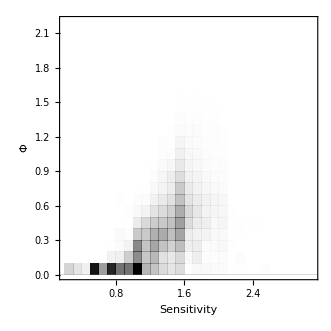

```mathematica
imgAll=DensityHistogram[{Flatten[S,1],Mean/@Flatten[Φ,1]}ᵀ,PlotTheme->"Scientific",PerformanceGoal->"Speed",FrameLabel->{"Sensitivity","Φ"},ColorFunction->Function[{height},Opacity[height]],ChartBaseStyle->Black]
```

### fit

```mathematica
Clear[f]
```

```mathematica
sloop[data_]:=Module[{f},
f=LinearModelFit[data,x,x];
f["BestFitParameters"]⟦2⟧
]
```

```mathematica
sloops=sloop[{S⟦#⟧,Mean/@(Φ⟦#⟧)}ᵀ]&/@Range[1,100];
```

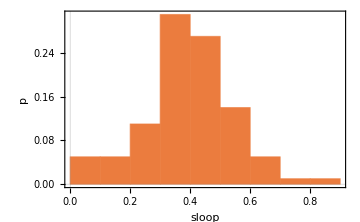

```mathematica
sloopsImage=Histogram[sloops,Automatic,"Probability",PlotTheme->"Scientific",FrameLabel->{"sloop",p},ImageSize->Medium]
```

### Export

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images","imgAllBoxWhisker.pdf"}],imgAllBoxWhisker]
```

/Users/yanbozhang/项目 & 存档/01 科研项目/IIT/IIT and Sensitivity/images/imgAllBoxWhisker.pdf

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images","imgAllBoxWhisker2.pdf"}],imgAllBoxWhisker2]
```

/Users/yanbozhang/项目 & 存档/01 科研项目/IIT/IIT and Sensitivity/images/imgAllBoxWhisker2.pdf

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images","imgAll.pdf"}],imgAll]
```

/Users/yanbozhang/项目 & 存档/01 科研项目/IIT/IIT and Sensitivity/images/imgAll.pdf

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images","fixedFunctions.pdf"}],fixedFunctions]
```

/Users/yanbozhang/项目 & 存档/01 科研项目/IIT/IIT and Sensitivity/images/fixedFunctions.pdf

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images","sloops.pdf"}],sloopsImage]
```

/Users/yanbozhang/项目 & 存档/01 科研项目/IIT/IIT and Sensitivity/images/sloops.pdf